Computational Physics

# Title. Black-body and Maxwellian Distribution

Paul Abbott

School of Physics, M013
The University of Western Australia
35 Stirling Highway
Crawley WA 6009, Australia

paul@physics.uwa.edu.au
physics.uwa.edu.au/~paul

#### Pre-requisites

We modify Equal so that Listable operations are automatically applied to both sides of any equality:

```mathematica
Unprotect[Equal];
```

```mathematica
listableQ(f_):=MemberQ(Attributes(f),Listable)
```

```mathematica
Equal/: lhs:f_Symbol?listableQ[___, _Equal, ___] :=
        Thread[ Unevaluated[lhs], Equal ]
```

```mathematica
Protect[Equal];
```

Now, we can directly manipulate equations.

Title.Section. Black-body Radiator

A blackbody (perfect radiator) emits energy according to the Planck equation:

```mathematica
P(ω_)=ℏ/(4 π^2 c^2)ω^3/(ⅇ^((ℏ ω)/(k T))-1);
```

where P(ω) ⅆω is the power emitted per unit area into the (angular) frequency range ω to ω + ⅆω.

Title.Section.Exercise. Compute exactly the total power emitted per unit area by integration over all frequencies. What is the law that results? [2]

```mathematica
Subscript[P, Total](T_)=Simplify[∫_0^∞ P(ω)ⅆω,ℏ/(k T)>0]
```

(k^4 π^2 T^4)/(60 c^2 ℏ^3)

This is the Stefan-Boltzmann law.

Title.Section.Exercise. The luminous efficiency, ℰ, is defined as the ratio of the power radiated in the visible spectrum (400 nm <λ< 700 nm) to the total power. Compute the luminous efficiency and plot it as a function of temperature over 2×10^3 K<T<2×10^4 K.  Use the constants in PhysicalConstants`. [5]

Compute the exact luminous efficiency, ℰ, for an arbitrary wavelength range.

```mathematica
p(ω_)=∫P(ω)ⅆω
```

(ℏ ((6 k^4 Li_4(ⅇ^((ω ℏ)/(k T))) T^4)/ℏ^4-(6 k^3 ω Li_3(ⅇ^((ω ℏ)/(k T))) T^3)/ℏ^3+(3 k^2 ω^2 Li_2(ⅇ^((ω ℏ)/(k T))) T^2)/ℏ^2+(k ω^3 log(1-ⅇ^((ω ℏ)/(k T))) T)/ℏ-ω^4/4))/(4 c^2 π^2)

```mathematica
ℰ[α_,β_][T_]=(p(β)-p(α))/(Subscript[P, Total](T))//Simplify
```

(15 (-24 k^4 Li_4(ⅇ^((α ℏ)/(k T))) T^4+24 k^4 Li_4(ⅇ^((β ℏ)/(k T))) T^4+24 k^3 α ℏ Li_3(ⅇ^((α ℏ)/(k T))) T^3-24 k^3 β ℏ Li_3(ⅇ^((β ℏ)/(k T))) T^3-12 k^2 α^2 ℏ^2 Li_2(ⅇ^((α ℏ)/(k T))) T^2+12 k^2 β^2 ℏ^2 Li_2(ⅇ^((β ℏ)/(k T))) T^2-4 k α^3 ℏ^3 log(1-ⅇ^((α ℏ)/(k T))) T+4 k β^3 ℏ^3 log(1-ⅇ^((β ℏ)/(k T))) T+α^4 ℏ^4-β^4 ℏ^4))/(4 k^4 π^4 T^4)

Write the required constants as replacement rules.

```mathematica
<<PhysicalConstants`
```

```mathematica
consts=Thread[{c,ℏ,k}->{SpeedOfLight,PlanckConstantReduced,BoltzmannConstant}]
```

{c→(299792458 Meter)/Second,ℏ→1.05457×10^-34 Joule Second,k→(1.38065×10^-23 Joule)/Kelvin}

In the range, λ_1=400 nm <λ< λ_2=700 nm, we have

```mathematica
Subscript[λ, 1]=400×10^-9 Meter;
```

```mathematica
Subscript[λ, 2]=700×10^-9 Meter;
```

and the dimensionless luminous efficiency is

```mathematica
ℰ[T_]=ℰ[(2 π c)/Subscript[λ, 2],(2 π c)/Subscript[λ, 1]][T Kelvin]/.consts//Simplify
```

1/T^4(-0.923938 Li_4(ⅇ^(20553.9/T)) T^4+0.923938 Li_4(ⅇ^(35969.4/T)) T^4+18990.6 Li_3(ⅇ^(20553.9/T)) T^3-33233.5 Li_3(ⅇ^(35969.4/T)) T^3-1.95165×10^8 Li_2(ⅇ^(20553.9/T)) T^2+5.97694×10^8 Li_2(ⅇ^(35969.4/T)) T^2-1.33714×10^12 log(1-ⅇ^(20553.9/T)) T+7.16623×10^12 log(1-ⅇ^(35969.4/T)) T-5.75703×10^16)

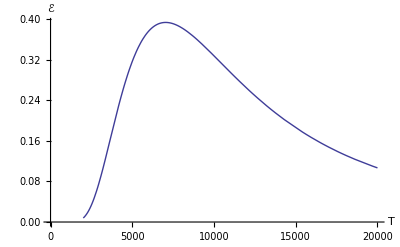

```mathematica
Plot[ℰ(T),{T,2 ×10^3,20× 10^3},AxesLabel->{T,ℰ},WorkingPrecision->20,PlotPoints->5,AxesOrigin->{0,0}]
```

Title.Section.Exercise. Compute the luminous efficiency of an incandescent light bulb (Hint: look up the melting point of Tungsten). What would you need to do to generate visible light more efficiently? [3]

The melting point of Tungsten is 3655 K (See CRC Handbook of Chemistry and Physics, CRC Press, Florida, 1978, E-213) so we compute

```mathematica
ℰ[3655]//Chop
```

0.163296

The luminous efficiency of an maximum incandescent light bulb is around 16%. If we can go to a higher temperature we could improve the luminous efficiency.

Title.Section.Exercise. At what temperature is the luminous efficiency a maximum? Compare this value with the surface temperature of the sun and comment. [3]

Use FindMaximum and the secant method by supplying a pair of starting values:

```mathematica
FindMaximum[Re[ℰ[T]],{T,6000,6100}]
```

{0.393021,{T→7042.18}}

The maximum efficiency is about 39% at 7042K. The surface temperature of the sun is 5776K (Source: CRC Handbook of Chemistry and Physics, CRC Press, Florida, 1978, F-180) so this is greater than (but of similar order to) this value.

One can use Dt (the total differential) to automatically handle a change of variables. For example, in ⅆx/(a^2+x^2) we can compute the change variables x→a tan(θ) as follows. First declare that a is a constant (using UpSet rather than Set),

```mathematica
Dt[a]^=0;
```

and then use the replacement rule x→a tan(θ).

```mathematica
Dt[x]/(a^2+x^2)/.x->a tan(θ)//Simplify
```

ⅆθ/a

Title.Section.Exercise. Compute and then plot the power emitted per unit area as a function of wavelength, λ, at the surface temperature of the sun (Hint: you need to do the change of variables from ω→2π c/λ. You might want to compare your answer to e.g., Robert Resnick, Basic Concepts: Relativity and Early Quantum Theory, Wiley, New York, 1972, pp113-124). What wavelengths (hence colours) correspond to the maximum and half-maximum (there are 2 values) at this temperature? Comment on your result. [6]

Use Dt to automatically handle the change of variables:

```mathematica
Dt[c]^=0;
```

```mathematica
p(λ_)=-(P(ω) Dt[ω])/Dt[λ]/.ω->(2 π c)/λ
```

(4 c^2 π^2 ℏ)/((-1+ⅇ^((2 c π ℏ)/(k T λ))) λ^5)

Hence the luminuous efficiency as a function of λ at the surface temperature of the sun is

```mathematica
SunLE[λ_]=(p(λ Meter))/(Joule Meter^-3)Second/.consts/.T->5776 Kelvin;
```

Determine the maximum power and corresponding wavelength.

```mathematica
FindMaximum[SunLE[λ],{λ,10^-7,2×10^-7}]
```

{8.27206×10^13,{λ→5.01691×10^-7}}

```mathematica
λmax=λ/.Last[%]
```

5.01691×10^-7

Determine the two half-maximum values.

```mathematica
Subscript[λ, 1]=λ/.FindRoot[SunLE[λ]==SunLE[λmax]/2,{λ,2.5×10^-7},AccuracyGoal->2]
```

3.07654×10^-7

```mathematica
Subscript[λ, 2]=λ/.FindRoot[SunLE[λ]==SunLE[λmax]/2,{λ,10^-6},AccuracyGoal->2]
```

9.11573×10^-7

Plot the luminuous efficiency as a function of λ and also show the two half-maximum values.

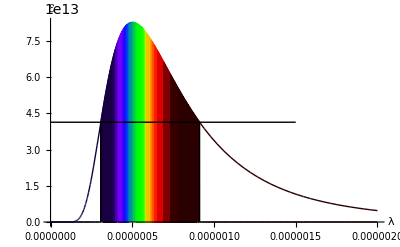

```mathematica
Plot[Evaluate[{ 1,Boole[Subscript[λ, 1]<λ<Subscript[λ, 2]]}SunLE(λ)],{λ,0,2×10^-6},PlotRange->All,AxesLabel->{λ,ℰ},Epilog->{Line[({{Subscript[λ, 1], 0}, {Subscript[λ, 1], SunLE(Subscript[λ, 1])}})],Line[({{Subscript[λ, 2], 0}, {Subscript[λ, 2], SunLE(Subscript[λ, 2])}})],Line[({{0, SunLE(Subscript[λ, 1])}, {1.5×10^-6, SunLE(Subscript[λ, 1])}})]},Filling->{2->Axis},ColorFunction:>(ColorData["VisibleSpectrum"][10^9#]&),ColorFunctionScaling->False]
```

So, in terms of the FWHM, the wavelength range is 308nm<λ<912nm “centred” on 502nm. The majority of the power output is in the visible with significant power at the UV and IR ends of the spectrum. Note that this is the power output per unit area from the sun's surface—not the power received at the earth's surface. The atmosphere does not transmit all wavelengths with equal absorption.

## Title.Section. Maxwellian Speed Distribution

Consider producing a specified probability distribution function (pdf). In this exercise you will generate random numbers with a (normalized) Maxwellian pdf, which describes the distribution of molecular speeds (see any standard physics text, e.g, D Halliday, R Resnick, J Walker, Fundamentals of Physics, (4th ed, Wiley, New York, 1993)).

Title.Section.Exercise. The Maxwellian pdf is  v^2 ⅇ^(-a v^2). Compute the normalized Maxwellian pdf. (Hint: normalise by dividing by ∫_0^∞ v^2 ⅇ^(-a v^2)ⅆv). [2]

```mathematica
pdf[a_][v_]=Simplify[(v^2 ⅇ^(-a v^2))/(∫_0^∞ v^2 ⅇ^(-a v^2)ⅆv),a>0]
```

(4 a^(3/2) ⅇ^(-a v^2) v^2)/(√π)

Built-in

```mathematica
PDF[MaxwellDistribution[1/(√(2a))],v]
```

Piecewise[{{(4 a^(3/2) v^2 ⅇ^(-a v^2))/(√π), v>0}, {0, True}}]

Title.Section.Exercise. Plot the normalized Maxwellian pdf for a=0.1, 0.5,1. [2]

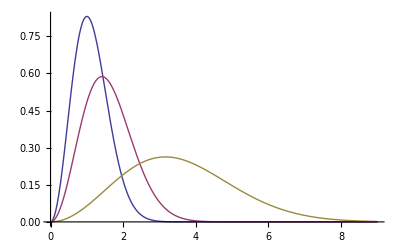

```mathematica
Plot[Evaluate[Through[(pdf/@{1,0.5,0.1})[v]]],{v,0,9},PlotRange->All]
```

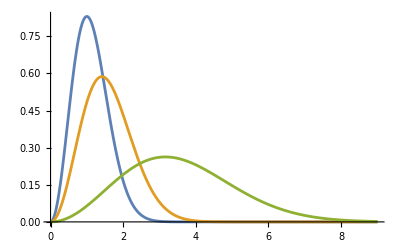

```mathematica
Plot[Evaluate[(a↦PDF[MaxwellDistribution[1/(√(2a))],v])/@{1,0.5,0.1}],{v,0,9},PlotRange->All]
```

Note that a “universal” PDF is obtained as a function of v/√a (identical to putting a=1):

```mathematica
𝒫[v_]=1/(√a)pdf[a][v/(√a)]
```

(4 ⅇ^(-v^2) v^2)/(√π)

```mathematica
pdf[1][v]
```

(4 ⅇ^(-v^2) v^2)/(√π)

To generate random numbers according to a pdf, we first need to obtain the cumulative distribution function (cdf), then find the inverse cdf and apply it to a uniformly distributed random number in the range [0,1]. (See Chapter 26.8 of Handbook of Mathematical Functions, edited by M. Abramowitz and I. Stegun.)

Title.Section.Exercise. Compute and plot the Maxwellian cdf. Note that a “universal” CDF is obtained by rescaling v→v/√a. [2]

Since v→v/√a⇒ⅆv→ⅆv/√a, is the “universal” CDF.

```mathematica
cdf(v_)=√a∫_0^(v/(√a)) 1/(√a)pdf[a][v]ⅆv//Simplify
```

erf(v)-(2 ⅇ^(-v^2) v)/(√π)

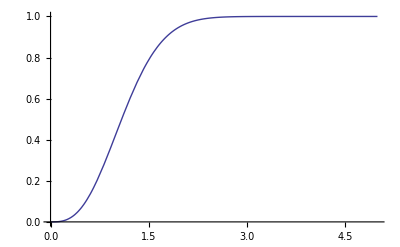

```mathematica
Plot[cdf(w),{w,0,5}]
```

An easy way to numerically construct the inverse cdf is to extract the list of Plot coordinates to produce a table of values:

```mathematica
values=Cases[First[Plot[cdf(w),{w,0,5}]],Line[{x__}]->x,∞]
```

(1.02041×10^-7 | 8.07328×10^-22
0.00153359 | 2.71326×10^-9
0.00306708 | 2.17038×10^-8
0.00460056 | 7.32473×10^-8
0.00613405 | 1.73619×10^-7
0.00766754 | 3.39091×10^-7
0.00920103 | 5.85937×10^-7
0.0107345 | 9.30424×10^-7
0.012268 | 1.38882×10^-6
0.0138015 | 1.97739×10^-6
0.015335 | 2.71239×10^-6
0.0168685 | 3.61008×10^-6
0.018402 | 4.6867×10^-6
0.0199354 | 5.95851×10^-6
0.0214689 | 7.44174×10^-6
0.0230024 | 9.15264×10^-6
0.0245359 | 0.0000111074
0.0260694 | 0.0000133223
0.0276029 | 0.0000158135
0.0291364 | 0.0000185973
0.0306699 | 0.0000216897
0.0322033 | 0.0000251071
0.0337368 | 0.0000288656
0.0352703 | 0.0000329813
0.0368038 | 0.0000374705
0.0383373 | 0.0000423492
0.0398708 | 0.0000476336
0.0414043 | 0.0000533399
0.0429378 | 0.0000594842
0.0444712 | 0.0000660825
0.0460047 | 0.0000731509
0.0490717 | 0.0000887626
0.0506052 | 0.0000973379
0.0521387 | 0.000106448
0.0552057 | 0.000126334
0.0567391 | 0.000137143
0.0582726 | 0.00014855
0.0613396 | 0.000173223
0.0628731 | 0.000186521
0.0644066 | 0.000200481
0.0674736 | 0.000230451
0.069007 | 0.000246492
0.0705405 | 0.000263259
0.0736075 | 0.000299033
0.075141 | 0.000318071
0.0766745 | 0.000337897
0.0797415 | 0.000379979
0.0812749 | 0.000402266
0.0828084 | 0.000425404
0.0858754 | 0.000474296
0.0874089 | 0.000500081
0.0889424 | 0.00052678
0.0920094 | 0.000582982
0.0981433 | 0.000707029
0.0998058 | 0.000743424
0.101468 | 0.00078104
0.104793 | 0.00086001
0.111443 | 0.00103345
0.113106 | 0.00108015
0.114768 | 0.00112823
0.118093 | 0.00122859
0.124743 | 0.00144664
0.126405 | 0.00150488
0.128068 | 0.00156464
0.131393 | 0.00168882
0.138043 | 0.00195634
0.139705 | 0.00202732
0.141368 | 0.00209997
0.144693 | 0.00225037
0.151343 | 0.00257209
0.153005 | 0.00265698
0.154667 | 0.0027437
0.157992 | 0.00292266
0.164642 | 0.00330321
0.166305 | 0.00340316
0.167967 | 0.00350508
0.171292 | 0.00371488
0.177942 | 0.00415877
0.179605 | 0.0042749
0.181267 | 0.00439314
0.184592 | 0.00463598
0.191242 | 0.00514758
0.204542 | 0.00627819
0.206094 | 0.00641977
0.207646 | 0.00656341
0.210751 | 0.00685691
0.21696 | 0.00746916
0.229379 | 0.0087974
0.230931 | 0.00897339
0.232483 | 0.00915164
0.235588 | 0.00951495
0.241797 | 0.0102691
0.254216 | 0.0118903
0.255768 | 0.0121037
0.25732 | 0.0123196
0.260425 | 0.0127587
0.266634 | 0.0136666
0.279053 | 0.0156035
0.303889 | 0.019979
0.305411 | 0.0202695
0.306933 | 0.0205627
0.309977 | 0.0211569
0.316064 | 0.0223773
0.328239 | 0.0249479
0.329761 | 0.0252815
0.331283 | 0.0256178
0.334327 | 0.0262989
0.340414 | 0.0276943
0.352589 | 0.03062
0.354111 | 0.0309985
0.355633 | 0.0313799
0.358676 | 0.0321511
0.364764 | 0.0337282
0.376939 | 0.0370215
0.401288 | 0.0441733
0.402939 | 0.0446858
0.40459 | 0.0452018
0.407892 | 0.0462444
0.414495 | 0.0483721
0.427702 | 0.0527984
0.454115 | 0.0623394
0.455766 | 0.0629664
0.457417 | 0.0635969
0.460719 | 0.0648688
0.467322 | 0.0674559
0.480529 | 0.0728035
0.506942 | 0.0841907
0.508483 | 0.0848833
0.510024 | 0.0855791
0.513105 | 0.0869798
0.519268 | 0.0898188
0.531593 | 0.0956453
0.556244 | 0.107888
0.605546 | 0.134672
0.607215 | 0.135631
0.608885 | 0.136594
0.612224 | 0.138529
0.618903 | 0.142439
0.63226 | 0.150415
0.658975 | 0.166977
0.712404 | 0.202387
0.817314 | 0.279398
0.915173 | 0.357512
1.02129 | 0.445261
1.12035 | 0.52658
1.21746 | 0.60286
1.32283 | 0.67921
1.42115 | 0.742754
1.42282 | 0.74376
1.42448 | 0.744764
1.42781 | 0.746764
1.43448 | 0.750734
1.4478 | 0.758559
1.47444 | 0.77374
1.52773 | 0.802206
1.52936 | 0.803039
1.531 | 0.80387
1.53427 | 0.805525
1.54081 | 0.808806
1.55388 | 0.815253
1.58004 | 0.827694
1.63235 | 0.850778
1.63388 | 0.851415
1.6354 | 0.852051
1.63845 | 0.853316
1.64455 | 0.855822
1.65675 | 0.860739
1.68114 | 0.870201
1.68266 | 0.870776
1.68419 | 0.87135
1.68724 | 0.87249
1.69334 | 0.874749
1.70553 | 0.879175
1.72993 | 0.887672
1.73158 | 0.888231
1.73323 | 0.888788
1.73654 | 0.889896
1.74316 | 0.892085
1.75638 | 0.896364
1.78284 | 0.904526
1.7845 | 0.905019
1.78615 | 0.90551
1.78946 | 0.906486
1.79607 | 0.908415
1.8093 | 0.912178
1.83576 | 0.919337
1.8373 | 0.91974
1.83884 | 0.920141
1.84193 | 0.920939
1.8481 | 0.922515
1.86045 | 0.925593
1.88515 | 0.931453
1.88669 | 0.931806
1.88823 | 0.932158
1.89132 | 0.932858
1.89749 | 0.934239
1.90984 | 0.936933
1.93454 | 0.942051
1.93621 | 0.942385
1.93788 | 0.942718
1.94123 | 0.943377
1.94792 | 0.944679
1.96129 | 0.947207
1.98805 | 0.951977
1.98973 | 0.952263
1.9914 | 0.952548
1.99474 | 0.953112
2.00143 | 0.954225
2.01481 | 0.956383
2.04157 | 0.960446
2.04321 | 0.960684
2.04485 | 0.960921
2.04814 | 0.961392
2.05471 | 0.96232
2.06784 | 0.964119
2.09411 | 0.967499
2.09576 | 0.967701
2.0974 | 0.967901
2.10068 | 0.9683
2.10725 | 0.969084
2.12038 | 0.970603
2.14666 | 0.97345
2.14819 | 0.973609
2.14972 | 0.973766
2.15278 | 0.974079
2.15891 | 0.974695
2.17116 | 0.975889
2.19567 | 0.978132
2.19721 | 0.978266
2.19874 | 0.978399
2.2018 | 0.978663
2.20793 | 0.979184
2.22018 | 0.980191
2.24469 | 0.982079
2.24635 | 0.982201
2.24801 | 0.982323
2.25133 | 0.982563
2.25798 | 0.983036
2.27126 | 0.983947
2.29784 | 0.985641
2.2995 | 0.985742
2.30116 | 0.985842
2.30448 | 0.986039
2.31112 | 0.986428
2.32441 | 0.987176
2.35098 | 0.988564
2.35253 | 0.98864
2.35408 | 0.988717
2.35718 | 0.988868
2.36339 | 0.989165
2.37579 | 0.989737
2.4006 | 0.990802
2.40215 | 0.990866
2.4037 | 0.990928
2.4068 | 0.991053
2.413 | 0.991297
2.42541 | 0.991768
2.45022 | 0.992641
2.45174 | 0.992692
2.45326 | 0.992742
2.4563 | 0.992842
2.46238 | 0.993038
2.47454 | 0.993416
2.49886 | 0.994116
2.50038 | 0.994158
2.5019 | 0.994199
2.50495 | 0.994281
2.51103 | 0.994441
2.52319 | 0.994749
2.54751 | 0.995319
2.54916 | 0.995356
2.55081 | 0.995392
2.55411 | 0.995464
2.5607 | 0.995604
2.5739 | 0.995874
2.60028 | 0.996368
2.60193 | 0.996397
2.60358 | 0.996426
2.60688 | 0.996483
2.61348 | 0.996594
2.62667 | 0.996808
2.65306 | 0.997198
2.65459 | 0.99722
2.65613 | 0.997241
2.65921 | 0.997283
2.66537 | 0.997365
2.67768 | 0.997523
2.7023 | 0.997813
2.70384 | 0.99783
2.70538 | 0.997847
2.70846 | 0.99788
2.71461 | 0.997945
2.72693 | 0.998071
2.75155 | 0.998301
2.75322 | 0.998315
2.75489 | 0.99833
2.75822 | 0.998359
2.76489 | 0.998415
2.77824 | 0.998521
2.77991 | 0.998534
2.78157 | 0.998547
2.78491 | 0.998572
2.79158 | 0.998621
2.80492 | 0.998715
2.80659 | 0.998726
2.80826 | 0.998738
2.8116 | 0.99876
2.81827 | 0.998803
2.83161 | 0.998885
2.8583 | 0.999034
2.85994 | 0.999043
2.86157 | 0.999051
2.86485 | 0.999068
2.8714 | 0.9991
2.8845 | 0.999162
2.88614 | 0.99917
2.88778 | 0.999177
2.89105 | 0.999192
2.8976 | 0.99922
2.9107 | 0.999274
2.91234 | 0.999281
2.91398 | 0.999287
2.91725 | 0.9993
2.9238 | 0.999325
2.9369 | 0.999372
2.9631 | 0.999458
2.96463 | 0.999463
2.96616 | 0.999467
2.96921 | 0.999476
2.97532 | 0.999494
2.98754 | 0.999528
2.98907 | 0.999532
2.99059 | 0.999536
2.99365 | 0.999544
2.99976 | 0.99956
3.01198 | 0.999589
3.0135 | 0.999593
3.01503 | 0.999596
3.01809 | 0.999603
3.02419 | 0.999617
3.03641 | 0.999643
3.06085 | 0.99969
3.06251 | 0.999693
3.06416 | 0.999696
3.06748 | 0.999702
3.0741 | 0.999713
3.08735 | 0.999735
3.08901 | 0.999737
3.09067 | 0.99974
3.09398 | 0.999745
3.1006 | 0.999755
3.11385 | 0.999773
3.11551 | 0.999775
3.11717 | 0.999778
3.12048 | 0.999782
3.1271 | 0.99979
3.14036 | 0.999806
3.16686 | 0.999835
3.1684 | 0.999836
3.16995 | 0.999838
3.17304 | 0.999841
3.17923 | 0.999847
3.1916 | 0.999858
3.19314 | 0.999859
3.19469 | 0.999861
3.19778 | 0.999863
3.20396 | 0.999868
3.21633 | 0.999878
3.21788 | 0.999879
3.21943 | 0.99988
3.22252 | 0.999882
3.2287 | 0.999887
3.24107 | 0.999895
3.26581 | 0.99991
3.26733 | 0.999911
3.26884 | 0.999912
3.27187 | 0.999913
3.27794 | 0.999917
3.29006 | 0.999923
3.29158 | 0.999924
3.29309 | 0.999924
3.29613 | 0.999926
3.30219 | 0.999929
3.31431 | 0.999934
3.31583 | 0.999934
3.31735 | 0.999935
3.32038 | 0.999936
3.32644 | 0.999939
3.33857 | 0.999943
3.36282 | 0.999951
3.36446 | 0.999952
3.36611 | 0.999952
3.3694 | 0.999953
3.37598 | 0.999955
3.38913 | 0.999959
3.39078 | 0.99996
3.39242 | 0.99996
3.39571 | 0.999961
3.40229 | 0.999962
3.41545 | 0.999966
3.41709 | 0.999966
3.41874 | 0.999966
3.42203 | 0.999967
3.42861 | 0.999968
3.44176 | 0.999971
3.46808 | 0.999976
3.46961 | 0.999976
3.47115 | 0.999976
3.47422 | 0.999977
3.48035 | 0.999978
3.49263 | 0.999979
3.49417 | 0.99998
3.4957 | 0.99998
3.49877 | 0.99998
3.50491 | 0.999981
3.51718 | 0.999983
3.51872 | 0.999983
3.52025 | 0.999983
3.52332 | 0.999983
3.52946 | 0.999984
3.54174 | 0.999985
3.56629 | 0.999987
3.56795 | 0.999988
3.56962 | 0.999988
3.57294 | 0.999988
3.5796 | 0.999989
3.59291 | 0.99999
3.59457 | 0.99999
3.59623 | 0.99999
3.59956 | 0.99999
3.60621 | 0.999991
3.61952 | 0.999991
3.62119 | 0.999991
3.62285 | 0.999992
3.62618 | 0.999992
3.63283 | 0.999992
3.64614 | 0.999993
3.6478 | 0.999993
3.64947 | 0.999993
3.65279 | 0.999993
3.65945 | 0.999993
3.67275 | 0.999994
3.67431 | 0.999994
3.67586 | 0.999994
3.67897 | 0.999994
3.68518 | 0.999995
3.69761 | 0.999995
3.69916 | 0.999995
3.70071 | 0.999995
3.70382 | 0.999995
3.71004 | 0.999995
3.72246 | 0.999996
3.72402 | 0.999996
3.72557 | 0.999996
3.72868 | 0.999996
3.73489 | 0.999996
3.74732 | 0.999997
3.77217 | 0.999997
3.77369 | 0.999997
3.77522 | 0.999997
3.77826 | 0.999997
3.78435 | 0.999997
3.79654 | 0.999998
3.79806 | 0.999998
3.79958 | 0.999998
3.80263 | 0.999998
3.80872 | 0.999998
3.8209 | 0.999998
3.82243 | 0.999998
3.82395 | 0.999998
3.82699 | 0.999998
3.83309 | 0.999998
3.84527 | 0.999998
3.84679 | 0.999998
3.84831 | 0.999998
3.85136 | 0.999998
3.85745 | 0.999998
3.86964 | 0.999999
3.87129 | 0.999999
3.87294 | 0.999999
3.87624 | 0.999999
3.88285 | 0.999999
3.89607 | 0.999999
3.89772 | 0.999999
3.89937 | 0.999999
3.90267 | 0.999999
3.90928 | 0.999999
3.9225 | 0.999999
3.92415 | 0.999999
3.9258 | 0.999999
3.9291 | 0.999999
3.93571 | 0.999999
3.94893 | 0.999999
3.95058 | 0.999999
3.95223 | 0.999999
3.95553 | 0.999999
3.96214 | 0.999999
3.97536 | 0.999999
3.9769 | 0.999999
3.97844 | 0.999999
3.98152 | 0.999999
3.98769 | 0.999999
4.00002 | 0.999999
4.00157 | 0.999999
4.00311 | 0.999999
4.00619 | 1.
4.01236 | 1.
4.02469 | 1.
4.02623 | 1.
4.02778 | 1.
4.03086 | 1.
4.03703 | 1.
4.04936 | 1.
4.0509 | 1.
4.05244 | 1.
4.05553 | 1.
4.06169 | 1.
4.07403 | 1.
4.0757 | 1.
4.07737 | 1.
4.08071 | 1.
4.08739 | 1.
4.10076 | 1.
4.1041 | 1.
4.10744 | 1.
4.11412 | 1.
4.12749 | 1.
4.13083 | 1.
4.13417 | 1.
4.14086 | 1.
4.15422 | 1.
4.15756 | 1.
4.1609 | 1.
4.16759 | 1.
4.18095 | 1.
4.18751 | 1.
4.19407 | 1.
4.2072 | 1.
4.21376 | 1.
4.22032 | 1.
4.23344 | 1.
4.24 | 1.
4.24656 | 1.
4.25969 | 1.
4.27281 | 1.
4.28593 | 1.
4.29817 | 1.
4.31041 | 1.
4.32265 | 1.
4.33489 | 1.
4.35937 | 1.
4.38386 | 1.
4.43695 | 1.
4.49004 | 1.
4.5396 | 1.
4.58917 | 1.
4.63776 | 1.
4.68635 | 1.
4.73907 | 1.
4.79179 | 1.
4.84098 | 1.
4.89017 | 1.
4.94349 | 1.
4.99681 | 1.
4.99841 | 1.
5. | 1.)

Alternatively, use Sow and Reap.

```mathematica
{plot,vals}=Reap@Plot[Sow[{w,cdf(w)}][[2]],{w,0,5}];plot
```

-Graphics-

```mathematica
values=Union@Sort[Drop[First@vals,{2,2}]]
```

(1.02041×10^-7 | 8.07328×10^-22
0.000102143 | 8.01656×10^-13
0.00153359 | 2.71326×10^-9
0.00306708 | 2.17038×10^-8
0.00460056 | 7.32473×10^-8
0.00613405 | 1.73619×10^-7
0.00766754 | 3.39091×10^-7
0.00920103 | 5.85937×10^-7
0.0107345 | 9.30424×10^-7
0.012268 | 1.38882×10^-6
0.0138015 | 1.97739×10^-6
0.015335 | 2.71239×10^-6
0.0168685 | 3.61008×10^-6
0.018402 | 4.6867×10^-6
0.0199354 | 5.95851×10^-6
0.0214689 | 7.44174×10^-6
0.0230024 | 9.15264×10^-6
0.0245359 | 0.0000111074
0.0260694 | 0.0000133223
0.0276029 | 0.0000158135
0.0291364 | 0.0000185973
0.0306699 | 0.0000216897
0.0322033 | 0.0000251071
0.0337368 | 0.0000288656
0.0352703 | 0.0000329813
0.0368038 | 0.0000374705
0.0383373 | 0.0000423492
0.0398708 | 0.0000476336
0.0414043 | 0.0000533399
0.0429378 | 0.0000594842
0.0444712 | 0.0000660825
0.0460047 | 0.0000731509
0.0490717 | 0.0000887626
0.0506052 | 0.0000973379
0.0521387 | 0.000106448
0.0552057 | 0.000126334
0.0567391 | 0.000137143
0.0582726 | 0.00014855
0.0613396 | 0.000173223
0.0628731 | 0.000186521
0.0644066 | 0.000200481
0.0674736 | 0.000230451
0.069007 | 0.000246492
0.0705405 | 0.000263259
0.0736075 | 0.000299033
0.075141 | 0.000318071
0.0766745 | 0.000337897
0.0797415 | 0.000379979
0.0812749 | 0.000402266
0.0828084 | 0.000425404
0.0858754 | 0.000474296
0.0874089 | 0.000500081
0.0889424 | 0.00052678
0.0920094 | 0.000582982
0.0981433 | 0.000707029
0.0998058 | 0.000743424
0.101468 | 0.00078104
0.104793 | 0.00086001
0.111443 | 0.00103345
0.113106 | 0.00108015
0.114768 | 0.00112823
0.118093 | 0.00122859
0.124743 | 0.00144664
0.126405 | 0.00150488
0.128068 | 0.00156464
0.131393 | 0.00168882
0.138043 | 0.00195634
0.139705 | 0.00202732
0.141368 | 0.00209997
0.144693 | 0.00225037
0.151343 | 0.00257209
0.153005 | 0.00265698
0.154667 | 0.0027437
0.157992 | 0.00292266
0.164642 | 0.00330321
0.166305 | 0.00340316
0.167967 | 0.00350508
0.171292 | 0.00371488
0.177942 | 0.00415877
0.179605 | 0.0042749
0.181267 | 0.00439314
0.184592 | 0.00463598
0.191242 | 0.00514758
0.204542 | 0.00627819
0.206094 | 0.00641977
0.207646 | 0.00656341
0.210751 | 0.00685691
0.21696 | 0.00746916
0.229379 | 0.0087974
0.230931 | 0.00897339
0.232483 | 0.00915164
0.235588 | 0.00951495
0.241797 | 0.0102691
0.254216 | 0.0118903
0.255768 | 0.0121037
0.25732 | 0.0123196
0.260425 | 0.0127587
0.266634 | 0.0136666
0.279053 | 0.0156035
0.303889 | 0.019979
0.305411 | 0.0202695
0.306933 | 0.0205627
0.309977 | 0.0211569
0.316064 | 0.0223773
0.328239 | 0.0249479
0.329761 | 0.0252815
0.331283 | 0.0256178
0.334327 | 0.0262989
0.340414 | 0.0276943
0.352589 | 0.03062
0.354111 | 0.0309985
0.355633 | 0.0313799
0.358676 | 0.0321511
0.364764 | 0.0337282
0.376939 | 0.0370215
0.401288 | 0.0441733
0.402939 | 0.0446858
0.40459 | 0.0452018
0.407892 | 0.0462444
0.414495 | 0.0483721
0.427702 | 0.0527984
0.454115 | 0.0623394
0.455766 | 0.0629664
0.457417 | 0.0635969
0.460719 | 0.0648688
0.467322 | 0.0674559
0.480529 | 0.0728035
0.506942 | 0.0841907
0.508483 | 0.0848833
0.510024 | 0.0855791
0.513105 | 0.0869798
0.519268 | 0.0898188
0.531593 | 0.0956453
0.556244 | 0.107888
0.605546 | 0.134672
0.607215 | 0.135631
0.608885 | 0.136594
0.612224 | 0.138529
0.618903 | 0.142439
0.63226 | 0.150415
0.658975 | 0.166977
0.712404 | 0.202387
0.817314 | 0.279398
0.915173 | 0.357512
1.02129 | 0.445261
1.12035 | 0.52658
1.21746 | 0.60286
1.32283 | 0.67921
1.42115 | 0.742754
1.42282 | 0.74376
1.42448 | 0.744764
1.42781 | 0.746764
1.43448 | 0.750734
1.4478 | 0.758559
1.47444 | 0.77374
1.52773 | 0.802206
1.52936 | 0.803039
1.531 | 0.80387
1.53427 | 0.805525
1.54081 | 0.808806
1.55388 | 0.815253
1.58004 | 0.827694
1.63235 | 0.850778
1.63388 | 0.851415
1.6354 | 0.852051
1.63845 | 0.853316
1.64455 | 0.855822
1.65675 | 0.860739
1.68114 | 0.870201
1.68266 | 0.870776
1.68419 | 0.87135
1.68724 | 0.87249
1.69334 | 0.874749
1.70553 | 0.879175
1.72993 | 0.887672
1.73158 | 0.888231
1.73323 | 0.888788
1.73654 | 0.889896
1.74316 | 0.892085
1.75638 | 0.896364
1.78284 | 0.904526
1.7845 | 0.905019
1.78615 | 0.90551
1.78946 | 0.906486
1.79607 | 0.908415
1.8093 | 0.912178
1.83576 | 0.919337
1.8373 | 0.91974
1.83884 | 0.920141
1.84193 | 0.920939
1.8481 | 0.922515
1.86045 | 0.925593
1.88515 | 0.931453
1.88669 | 0.931806
1.88823 | 0.932158
1.89132 | 0.932858
1.89749 | 0.934239
1.90984 | 0.936933
1.93454 | 0.942051
1.93621 | 0.942385
1.93788 | 0.942718
1.94123 | 0.943377
1.94792 | 0.944679
1.96129 | 0.947207
1.98805 | 0.951977
1.98973 | 0.952263
1.9914 | 0.952548
1.99474 | 0.953112
2.00143 | 0.954225
2.01481 | 0.956383
2.04157 | 0.960446
2.04321 | 0.960684
2.04485 | 0.960921
2.04814 | 0.961392
2.05471 | 0.96232
2.06784 | 0.964119
2.09411 | 0.967499
2.09576 | 0.967701
2.0974 | 0.967901
2.10068 | 0.9683
2.10725 | 0.969084
2.12038 | 0.970603
2.14666 | 0.97345
2.14819 | 0.973609
2.14972 | 0.973766
2.15278 | 0.974079
2.15891 | 0.974695
2.17116 | 0.975889
2.19567 | 0.978132
2.19721 | 0.978266
2.19874 | 0.978399
2.2018 | 0.978663
2.20793 | 0.979184
2.22018 | 0.980191
2.24469 | 0.982079
2.24635 | 0.982201
2.24801 | 0.982323
2.25133 | 0.982563
2.25798 | 0.983036
2.27126 | 0.983947
2.29784 | 0.985641
2.2995 | 0.985742
2.30116 | 0.985842
2.30448 | 0.986039
2.31112 | 0.986428
2.32441 | 0.987176
2.35098 | 0.988564
2.35253 | 0.98864
2.35408 | 0.988717
2.35718 | 0.988868
2.36339 | 0.989165
2.37579 | 0.989737
2.4006 | 0.990802
2.40215 | 0.990866
2.4037 | 0.990928
2.4068 | 0.991053
2.413 | 0.991297
2.42541 | 0.991768
2.45022 | 0.992641
2.45174 | 0.992692
2.45326 | 0.992742
2.4563 | 0.992842
2.46238 | 0.993038
2.47454 | 0.993416
2.49886 | 0.994116
2.50038 | 0.994158
2.5019 | 0.994199
2.50495 | 0.994281
2.51103 | 0.994441
2.52319 | 0.994749
2.54751 | 0.995319
2.54916 | 0.995356
2.55081 | 0.995392
2.55411 | 0.995464
2.5607 | 0.995604
2.5739 | 0.995874
2.60028 | 0.996368
2.60193 | 0.996397
2.60358 | 0.996426
2.60688 | 0.996483
2.61348 | 0.996594
2.62667 | 0.996808
2.65306 | 0.997198
2.65459 | 0.99722
2.65613 | 0.997241
2.65921 | 0.997283
2.66537 | 0.997365
2.67768 | 0.997523
2.7023 | 0.997813
2.70384 | 0.99783
2.70538 | 0.997847
2.70846 | 0.99788
2.71461 | 0.997945
2.72693 | 0.998071
2.75155 | 0.998301
2.75322 | 0.998315
2.75489 | 0.99833
2.75822 | 0.998359
2.76489 | 0.998415
2.77824 | 0.998521
2.77991 | 0.998534
2.78157 | 0.998547
2.78491 | 0.998572
2.79158 | 0.998621
2.80492 | 0.998715
2.80659 | 0.998726
2.80826 | 0.998738
2.8116 | 0.99876
2.81827 | 0.998803
2.83161 | 0.998885
2.8583 | 0.999034
2.85994 | 0.999043
2.86157 | 0.999051
2.86485 | 0.999068
2.8714 | 0.9991
2.8845 | 0.999162
2.88614 | 0.99917
2.88778 | 0.999177
2.89105 | 0.999192
2.8976 | 0.99922
2.9107 | 0.999274
2.91234 | 0.999281
2.91398 | 0.999287
2.91725 | 0.9993
2.9238 | 0.999325
2.9369 | 0.999372
2.9631 | 0.999458
2.96463 | 0.999463
2.96616 | 0.999467
2.96921 | 0.999476
2.97532 | 0.999494
2.98754 | 0.999528
2.98907 | 0.999532
2.99059 | 0.999536
2.99365 | 0.999544
2.99976 | 0.99956
3.01198 | 0.999589
3.0135 | 0.999593
3.01503 | 0.999596
3.01809 | 0.999603
3.02419 | 0.999617
3.03641 | 0.999643
3.06085 | 0.99969
3.06251 | 0.999693
3.06416 | 0.999696
3.06748 | 0.999702
3.0741 | 0.999713
3.08735 | 0.999735
3.08901 | 0.999737
3.09067 | 0.99974
3.09398 | 0.999745
3.1006 | 0.999755
3.11385 | 0.999773
3.11551 | 0.999775
3.11717 | 0.999778
3.12048 | 0.999782
3.1271 | 0.99979
3.14036 | 0.999806
3.16686 | 0.999835
3.1684 | 0.999836
3.16995 | 0.999838
3.17304 | 0.999841
3.17923 | 0.999847
3.1916 | 0.999858
3.19314 | 0.999859
3.19469 | 0.999861
3.19778 | 0.999863
3.20396 | 0.999868
3.21633 | 0.999878
3.21788 | 0.999879
3.21943 | 0.99988
3.22252 | 0.999882
3.2287 | 0.999887
3.24107 | 0.999895
3.26581 | 0.99991
3.26733 | 0.999911
3.26884 | 0.999912
3.27187 | 0.999913
3.27794 | 0.999917
3.29006 | 0.999923
3.29158 | 0.999924
3.29309 | 0.999924
3.29613 | 0.999926
3.30219 | 0.999929
3.31431 | 0.999934
3.31583 | 0.999934
3.31735 | 0.999935
3.32038 | 0.999936
3.32644 | 0.999939
3.33857 | 0.999943
3.36282 | 0.999951
3.36446 | 0.999952
3.36611 | 0.999952
3.3694 | 0.999953
3.37598 | 0.999955
3.38913 | 0.999959
3.39078 | 0.99996
3.39242 | 0.99996
3.39571 | 0.999961
3.40229 | 0.999962
3.41545 | 0.999966
3.41709 | 0.999966
3.41874 | 0.999966
3.42203 | 0.999967
3.42861 | 0.999968
3.44176 | 0.999971
3.46808 | 0.999976
3.46961 | 0.999976
3.47115 | 0.999976
3.47422 | 0.999977
3.48035 | 0.999978
3.49263 | 0.999979
3.49417 | 0.99998
3.4957 | 0.99998
3.49877 | 0.99998
3.50491 | 0.999981
3.51718 | 0.999983
3.51872 | 0.999983
3.52025 | 0.999983
3.52332 | 0.999983
3.52946 | 0.999984
3.54174 | 0.999985
3.56629 | 0.999987
3.56795 | 0.999988
3.56962 | 0.999988
3.57294 | 0.999988
3.5796 | 0.999989
3.59291 | 0.99999
3.59457 | 0.99999
3.59623 | 0.99999
3.59956 | 0.99999
3.60621 | 0.999991
3.61952 | 0.999991
3.62119 | 0.999991
3.62285 | 0.999992
3.62618 | 0.999992
3.63283 | 0.999992
3.64614 | 0.999993
3.6478 | 0.999993
3.64947 | 0.999993
3.65279 | 0.999993
3.65945 | 0.999993
3.67275 | 0.999994
3.67431 | 0.999994
3.67586 | 0.999994
3.67897 | 0.999994
3.68518 | 0.999995
3.69761 | 0.999995
3.69916 | 0.999995
3.70071 | 0.999995
3.70382 | 0.999995
3.71004 | 0.999995
3.72246 | 0.999996
3.72402 | 0.999996
3.72557 | 0.999996
3.72868 | 0.999996
3.73489 | 0.999996
3.74732 | 0.999997
3.77217 | 0.999997
3.77369 | 0.999997
3.77522 | 0.999997
3.77826 | 0.999997
3.78435 | 0.999997
3.79654 | 0.999998
3.79806 | 0.999998
3.79958 | 0.999998
3.80263 | 0.999998
3.80872 | 0.999998
3.8209 | 0.999998
3.82243 | 0.999998
3.82395 | 0.999998
3.82699 | 0.999998
3.83309 | 0.999998
3.84527 | 0.999998
3.84679 | 0.999998
3.84831 | 0.999998
3.85136 | 0.999998
3.85745 | 0.999998
3.86964 | 0.999999
3.87129 | 0.999999
3.87294 | 0.999999
3.87624 | 0.999999
3.88285 | 0.999999
3.89607 | 0.999999
3.89772 | 0.999999
3.89937 | 0.999999
3.90267 | 0.999999
3.90928 | 0.999999
3.9225 | 0.999999
3.92415 | 0.999999
3.9258 | 0.999999
3.9291 | 0.999999
3.93571 | 0.999999
3.94893 | 0.999999
3.95058 | 0.999999
3.95223 | 0.999999
3.95553 | 0.999999
3.96214 | 0.999999
3.97536 | 0.999999
3.9769 | 0.999999
3.97844 | 0.999999
3.98152 | 0.999999
3.98769 | 0.999999
4.00002 | 0.999999
4.00157 | 0.999999
4.00311 | 0.999999
4.00619 | 1.
4.01236 | 1.
4.02469 | 1.
4.02623 | 1.
4.02778 | 1.
4.03086 | 1.
4.03703 | 1.
4.04936 | 1.
4.0509 | 1.
4.05244 | 1.
4.05553 | 1.
4.06169 | 1.
4.07403 | 1.
4.0757 | 1.
4.07737 | 1.
4.08071 | 1.
4.08739 | 1.
4.10076 | 1.
4.1041 | 1.
4.10744 | 1.
4.11412 | 1.
4.12749 | 1.
4.13083 | 1.
4.13417 | 1.
4.14086 | 1.
4.15422 | 1.
4.15756 | 1.
4.1609 | 1.
4.16759 | 1.
4.18095 | 1.
4.18751 | 1.
4.19407 | 1.
4.2072 | 1.
4.21376 | 1.
4.22032 | 1.
4.23344 | 1.
4.24 | 1.
4.24656 | 1.
4.25969 | 1.
4.27281 | 1.
4.28593 | 1.
4.29817 | 1.
4.31041 | 1.
4.32265 | 1.
4.33489 | 1.
4.35937 | 1.
4.38386 | 1.
4.43695 | 1.
4.49004 | 1.
4.5396 | 1.
4.58917 | 1.
4.63776 | 1.
4.68635 | 1.
4.73907 | 1.
4.79179 | 1.
4.84098 | 1.
4.89017 | 1.
4.94349 | 1.
4.99681 | 1.
4.99841 | 1.
5. | 1.)

then reverse them, and interpolate the result:

```mathematica
Inversecdf=Interpolation[Reverse/@values]
```

InterpolatingFunction[(8.07328×10^-22 | 1.),<>]

After reading off the minimum and maximum ordinate values

```mathematica
{tmin,tmax}=Inversecdf⟦1,1⟧
```

{8.07328×10^-22,1.}

we can plot the inverse cdf:

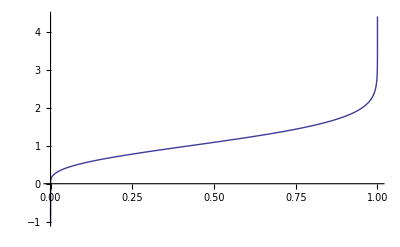

```mathematica
Plot[Inversecdf(t),{t,tmin,tmax},PlotRange->All]
```

Now that we have the inverse cdf we can apply it to a uniformly distributed random number in the range [0,1] to generate random numbers with a (normalized) Maxwellian pdf. We should verify that this process does indeed work properly.

Title.Section.Exercise. Produce a table of 20000 Maxwellian distributed random numbers,  “Bin” the data into bins of width δx=0.1. Verify that the binned data is normalized (i.e., the total area computed from the height and width of each bin sums to unity). [4]

Here is a table of 20000 Maxwellian distributed random numbers.

```mathematica
data=Inversecdf[RandomReal[{0,1},{20000}]];
```

“Bin” our data using BinCounts into bins of specified width:

```mathematica
δv=0.1;
```

to obtain the normalized frequencies,

```mathematica
fs=BinCounts[data,{0,Max[data],δv}]/(δv Length[data])
```

{0.0075,0.0555,0.1305,0.2405,0.3925,0.536,0.585,0.7545,0.7835,0.821,0.7985,0.809,0.71,0.6925,0.599,0.48,0.402,0.306,0.2545,0.183,0.1445,0.098,0.0795,0.0505,0.0325,0.0185,0.011,0.01,0.005,0.005,0.0005,0.0025,0.0005,0.0005,0,0}

the corresponding speeds,

```mathematica
vs=Range[δv/2,Max[data]-δv/2,δv];
```

and the width of each bin.

```mathematica
ws=Table[δv,{Length[fs]}];
```

Check that the binned data is normalized:

```mathematica
fs.ws
```

0.99995

Title.Section.Exercise. Compute the velocity expectation value, ⟨v⟩=∫_0^∞ p(v) vⅆv/∫_0^∞ p(v) ⅆv, and compare it to the numerical value obtained from the binned data.  [3]

The numerical (velocity) expectation value ⟨v⟩ is

```mathematica
(fs vs) .ws
```

1.12488

This should be compared to the exact value,

```mathematica
∫_0^∞ pdf[1][v] vⅆv
```

2/(√π)

```mathematica
N[%]
```

1.12838

The agreement is excellent.

Title.Section.Exercise. Compute the expectation value ⟨v^2⟩ numerically and analytically and compare them. [3]

Similarly, the expectation value ⟨v^2⟩

```mathematica
(fs vs^2).ws
```

1.49262

This should be compared to the exact value.

```mathematica
∫_0^∞ pdf[1][v] v^2 ⅆv
```

3/2

```mathematica
N[%]
```

1.5

Again, the agreement is excellent.

Title.Section.Exercise. Display a histogram of bar-chart of the binned data and compare to the exact distribution and comment. [3]

After loading the package

```mathematica
<<BarCharts`
```

we can produce a bar chart of our binned data and compare it with the exact distribution.

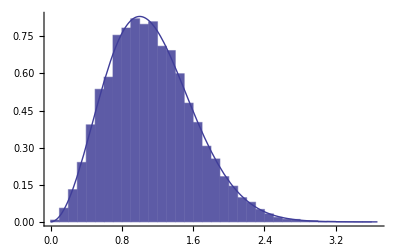

```mathematica
Show[GeneralizedBarChart[{vs, fs, ws}^T,PlotRange->All],Plot[pdf[1][v],{v,0,Max[data]}]]
```

There is excellent agreement.

Title.Section.Exercise. Use FindFit to see how well the binned data is fitted by the Maxwellian pdf. [3]

Check how well the data is fitted by the Maxwellian pdf:

```mathematica
FindFit[{vs, fs}^T,a pdf[b][v]+c,{a,b,c},v]
```

{a→0.995971,b→1.00424,c→0.00110788}